```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/412nm.dat"]
```

{{1.45287,-0.0797794},{1.39708,-0.188066},{1.35876,-0.258978},{1.32403,-0.322688},{1.28662,-0.347899},{1.25869,-0.360511},{1.22636,-0.372732},{1.19613,-0.351403},{1.17366,-0.371948},{1.15413,-0.427036},{1.12528,-0.49893},{1.11495,-0.377753},{1.10625,-0.361257},{1.09912,-0.326631},{1.09306,-0.265347},{1.0888,-0.242658},{1.08648,-0.264408},{1.08572,-0.291476},{1.08632,-0.453768},{1.0888,-0.485727},{1.09505,-0.320756},{1.09559,-0.280389},{1.12528,-0.16206},{1.14263,-0.0909537},{1.16354,-0.0200191},{1.19414,0.00129916},{1.22405,0.0180364},{1.25343,0.0228372},{1.28081,0.00886063},{1.31748,0.0149871},{1.36987,-0.000410084},{1.42194,-0.00817331},{1.47153,-0.054604},{1.11308,-0.15573}}

-1.07275+0.701152 x

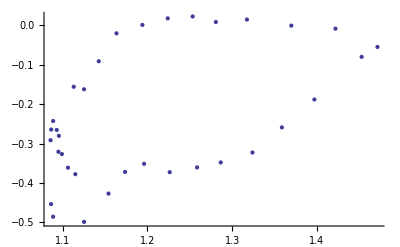

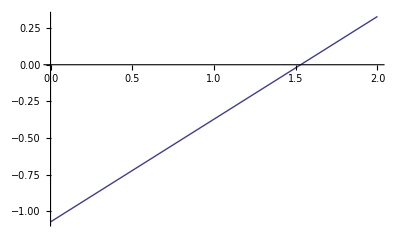

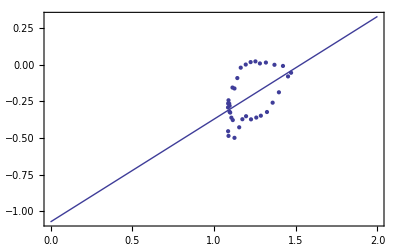

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```